# Unnamed functions and more complex functions

Math 213 - Math with Mathematica
Christopher Hanusa

## Overview

In this tutorial, we learn how Mathematica defines unnamed functions and how to develop more complex functions for one or more inputs.

## Defining an unnamed function

Let’s learn a more advanced way to define functions

Before we do that, let’s look at the internal format in which Mathematica defines a function.

### Using Function

Instead of defining our “square” and “addEmUp” functions like in the previous tutorial, we could have instead written:

```mathematica
alternateSquare=Function[x,x^2]
```

Function[x,x^2]

```mathematica
alternateAddEmUp=Function[{x,y},x+y]
```

Function[{x,y},x+y]

Then we can apply these functions in the same way.

```mathematica
alternateSquare[20]
```

400

```mathematica
alternateAddEmUp[-Pi,3Pi]
```

2 π

Here, we are using the Function command, which has two inputs.  The first input to Function is the input variable to the function (or list of input variables), and the second input to Function is the coder-defined output of the function.

NOTE: We used set (=) instead of set delayed (:=), and there was no need to use underscores.  All these things are taken into account by the Function command.

We can also apply a function written using a Function command without giving it a name.

```mathematica
Function[x,x^2][20]
```

400

```mathematica
Function[{x,y},x+y][2000,6994]
```

8994

This code is cumbersome, but it leads us to a widely used technique, that of unnamed functions.

### Unnamed functions

Suppose you want to code in a function that you only want to apply once and you don’t want to worry about giving it a name.  Then you can create an unnamed function.  They are a bit confusing at first, but become very handy as you become proficient.

(RHS[#])&   or   (RHS[#1,#2])&

(Again, RHS stands for Right Hand Side, and represents the actual function you want to apply to the variables.)

The # symbol represents an unnamed input variable.  While before you would define your right hand side around the input variable x, here wherever you would put x, you replace it by a # symbol. If your function has  more than one input, use #1, #2, #3, ... to represent the first, second, third, ... inputs in order.

The & symbol represents the end of the function and that signals to Mathematica that what follows should be the inputs to the function.

Often to increase readability, you can use parentheses ( ) to delimit the beginning and end of your unnamed function.

### Examples

The unnamed versions of the above functions are

```mathematica
(#^2)&
```

and

```mathematica
(#1+#2)&
```

Here are some examples of them in action:

```mathematica
(#^2)&[Pi]
```

π^2

```mathematica
(#1+#2)&[3,4]
```

7

Notice that when calling unnamed functions, you still need to use square brackets around the inputs.

## Comprehension Questions

### 1. For each of the following unnamed functions, write a sentence describing what it does. Find a suitable input (or inputs) and verify that the function does what you think it should.

```mathematica
(#^3+(#-1)^2)&
```

```mathematica
Range[Length[#]]&
```

```mathematica
#[[2]]&
```

### 2. Create an unnamed function that takes in an integer n and outputs the coordinate pair {x,y} where x is the n-th prime number and y is the (n+1)-st prime number.

### 3. Create an unnamed function that takes in three inputs and outputs one list with all three inputs in reverse order. (So for inputs 1, 4, 10, the output would be {10,4,1}.)

### 4. Create an unnamed function that takes in two inputs, (think: a function and a number) and then applies the first input to the second (think: it applies the inputted function to the inputted number)

### Solutions

#### Question 2.

```mathematica
{Prime[#],Prime[#+1]}&
```

#### Question 3.

```mathematica
{#3,#2,#1}&
```

#### Question 4.

```mathematica
#1[#2]&
```

## Unnamed functions and Map

An especially handy place to use unnamed functions is in tandem with the Map command. You might have a list of objects and want to apply a function to the whole list, but don’t especially want to define the function outright.  You can use the Map command and an unnamed function to do it!

Here is an example that squares all the entries in a list.

```mathematica
mylist=Range[4,17,3]
Map[#^2&,mylist]
```

{4,7,10,13,16}

{16,49,100,169,256}

And here is an example that creates regular polygons with the number of sides of the entries in the list.


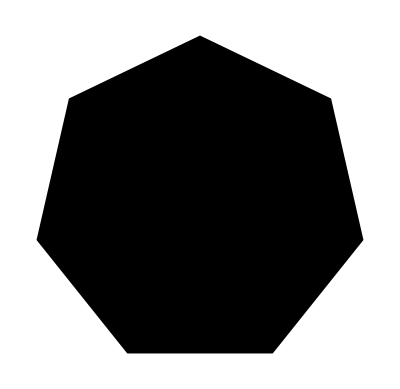
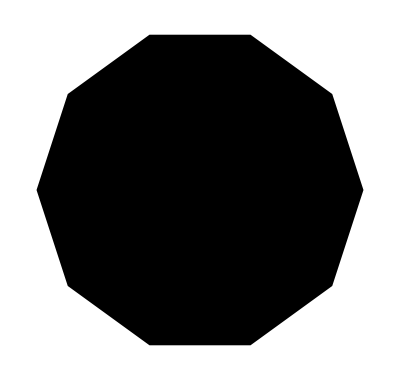
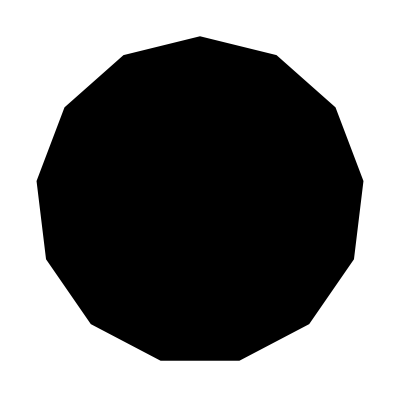
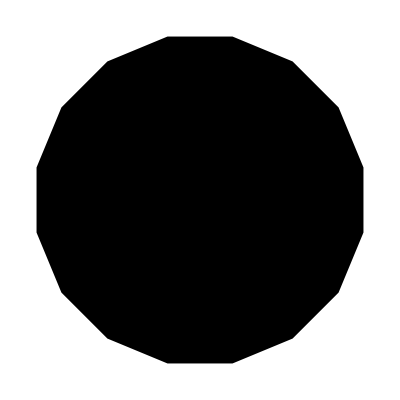

```mathematica
Map[Graphics[RegularPolygon[#]]&, mylist]
```

## MapThread

Map is used to apply a function (that takes one input) to each element in a list of objects.

When your function takes multiple inputs, and you want more than one of those inputs to vary, you need to use MapThread instead.

### Syntax

Suppose your function takes in three inputs, x, y, and z:

```mathematica
function[x_,y_,z_]:=x^2+y^2+z^2
```

And you have a list of x-values, a list of y-values, and a list of z-values, ALL OF THE SAME LENGTH!

```mathematica
xlist=Range[10]
ylist=RandomInteger[{1,10},10]
zlist=Range[10,1,-1]
```

{1,2,3,4,5,6,7,8,9,10}

{5,9,1,3,9,10,7,5,10,2}

{10,9,8,7,6,5,4,3,2,1}

Then to evaluate the function with the first input in each list, then the second input in each list, then the third input in each list, etcetera, use MapThread.  MapThread takes two inputs:  the first input is the function that will be applied and the second input is a list of the input lists.  (Read that again to make sure you understand what it is saying.)

Here is the continuation of the above example, in which we use MapThread to calculate f(x_1,y_1,z_1) then f(x_2,y_2,z_2) then f(x_3,y_3,z_3) through f(x_10,y_10,z_10).

```mathematica
MapThread[function,{xlist,ylist,zlist}]
```

{126,166,74,74,142,161,114,98,185,105}

This is equivalent to the following more complex code:

```mathematica
Table[function[xlist[[i]],ylist[[i]],zlist[[i]]],{i,1,Length[xlist]}]
```

{126,166,74,74,142,161,114,98,185,105}

### Examples

Example:  Suppose you want to calculate Sin[0], Cos[Pi/3], Tan[2Pi/3], Cot[Pi], Sec[4Pi/3] and Csc[5Pi/3].

First create the following two lists:

```mathematica
flist={Sin,Cos,Tan,Cot,Sec,Csc}
angleList=Range[0,5Pi/3,Pi/3]
```

{Sin,Cos,Tan,Cot,Sec,Csc}

{0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3}

Then we want to calculate f_1[angle_1], f_2[angle_2], ... , f_6[angle_6] so we use MapThread, with the unnamed function #1[#2]& (This applies the first input to the second function.)

```mathematica
MapThread[#1[#2]&,{flist,angleList}]
```

{0,1/2,-√3,ComplexInfinity,-2,-2/(√3)}

Example:  Suppose you want some colorful days of the week.   (To add color or other font styling, we use the Style function.)

```mathematica
words={"Monday","Tuesday","Wednesday","Thursday","Friday"};
colors={Red,Orange,Yellow,Green,Blue};
MapThread[Style[#1,#2]&,{words,colors}]
```

{Monday,Tuesday,Wednesday,Thursday,Friday}

## Comprehension Questions

### 5. Before evaluating the following lines of code, anticipate what will be the result will be. After evaluating the code, understand why the output is what it is and compare it with your expectations. If there was an error, figure out what needs to be done to correct it.

#### (a)

```mathematica
Map[#[[2]]&,{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

#### (b)

```mathematica
Map[{#,#^2},Range[1,9,2]]
```

#### (c)

```mathematica
Map[Plot[x^#,{x,0,5}]&,{2,5,7}]
```

#### (d)

```mathematica
MapThread[#1^#2&,{Range[5],Range[5]}]
```

#### (e)

```mathematica
xlist={12,11,10,9}; 
ylist={1,2,3,4,5};
MapThread[(#1-#2)&,{xlist,ylist}]
```

#### (f)

```mathematica
alist=Range[0,Pi,Pi/6];
blist=Range[0,2Pi,Pi/3];
MapThread[Sin[#1]Cos[#2]&,alist,blist]
```

### 6. Use the function you created for Question 2 above to create a list of the coordinate pairs of {prime #n, prime #(n+1)} for n from 1 to 20. Then display these coordinate pairs as a connected scatterplot.

### 7. Use Append to change the following coordinate pairs into coordinate triples by putting a zero into the third coordinate.

```mathematica
coords2D=Table[{i,i^2},{i,10}]
```

### Solutions

#### Question 5.

(b) You are missing the &.
(e) The lists xlist and ylist are not the same length.
(f) The lists alist and blist must be in a list.

#### Question 6.

```mathematica
ListLinePlot[Map[{Prime[#],Prime[#+1]}&,Range[20]]]
```

#### Question 7.

```mathematica
coords3D=Map[Append[#,0]&,coords2D]
```

## Important Concept: Q

The computer can determine if the number you give it is even or odd.  
The command EvenQ is one of many Mathematica functions that ask a question (Q).  When you evaluate a number, EvenQ determines if the number is even or not.  Evaluate the next cell.

```mathematica
EvenQ[3]
EvenQ[4]
EvenQ[Sqrt[2]]
```

The command PrimeQ determines if a number is prime.  Evaluate the next cell.

```mathematica
PrimeQ[1]
PrimeQ[55]
PrimeQ[97]
PrimeQ[1234577]
```

Go to the Documentation Center and search for ‘Q’ and focus on the built-in commands that end in Q, especially on the second page of results.  You will get a good feel for all the sorts of questions you can ask Mathematica to determine if a variable satisfies a property or not.

## Important Concept: If

It is often the case that you will want a function to do two things depending on whether a certain condition is true or false.  We will use the command If to do this.  The syntax for If is:

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

That is, you type If[condition,expression1,expression2], and Mathematica will first check the condition.  If the condition is True, then it will do expression1; otherwise it will do expression2.

```mathematica
z=10;
If[z^2<50,Print["z is small"],Print["z is large"]]
z=7;
If[z^2<50,Print["z is small"],Print["z is large"]]
```

### ! means negation

To change True to False or vice versa, use the ! operator.

```mathematica
!True
!False
!PrimeQ[77]
```

### == tests equality

If you are using an if statement that is testing equality, you need to use == instead of = because = is exclusively used to define variables.

Compare the following, the first defines x to be 4 and the second asks the question whether x is equal to 4.

```mathematica
x=4
```

4

```mathematica
x==4
```

True

## Comprehension Questions

### 8. Look at the following commands. Before you evaluate each of them, determine what you think the output of each of these commands will be. Then evaluate each command and see if you were correct. If you were incorrect, then ask a classmate and discuss.

```mathematica
!True
```

```mathematica
5!
```

```mathematica
If[x==2,3,5]
```

```mathematica
If[5>10,"Ra Ra Ra"]
```

```mathematica
If[IntegerQ[Pi],4,100]
```

```mathematica
Table[!OddQ[n],{n,1,10}]
```

```mathematica
Table[If[PrimeQ[n],1,0],{n,1,10}]
```

```mathematica
Table[If[PrimeQ[n],Print[n]],{n,1,10}];
```

### 9. Use an If statement to define a function abs that gives the absolute value of an input.

### 10. Define the function txp that takes as input an integer x and then outputs one of two things. If x is even, then output x/2. If x is odd, then output 3x+1.

## Important Concept: Module

When you are creating more complicated functions, you will need to use the Module function.

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

As you can see in the explanation of Module, it helps to quarantine the variables that you only use in this function.  This type of variables are called local variables.  As you can see in the following computation, even if i is defined outside the Module, you can use i inside without worrying about contamination.  It is good practice to define your functions in such a way that any variables you only use in your function are defined as local variables.

```mathematica
i=10;
Print["Outside Module, i is ",i]
Module[{i=20},Print["Inside Module, i is ",i]]
Print["Outside Module, i is ",i]
```

More importantly, Module lets you define a function that runs multiple lines of code in a row instead of just one line of code.  Each of these intermediate lines of code must end with a semicolon so that the each line of code is computed independently.  The output from the last line of code is the output of the whole Module command.

Here is an example that takes in two inputs, multiplies them together, then checks to see if this product is even or odd.  If the product is even, it divides by two.  If the product is odd, it subtracts one and then divides by two.  Then it checks to see if this result is prime or not, and displays either “Yay!” or “Bzzzz!”.  The output of this function is the list of the first result, second result, and third result.

```mathematica
manySteps[{x_,y_}]:=
 Module[{first,second,third},
first=x*y;
second=If[EvenQ[first],first/2,(first-1)/2];
third=If[PrimeQ[second],"Yay!","Bzzzz!"];
{first,second,third}]
```

Here are some examples of the results of this function, which you can check:

```mathematica
manySteps[{2,5}]
```

{10,5,Yay!}

```mathematica
manySteps[{3,5}]
```

{15,7,Yay!}

```mathematica
manySteps[{7,6}]
```

{42,21,Bzzzz!}

## Nest and NestList

If you want to iterate the same function on an input multiple times, use the Nest command.  If you want to see the intermediate results of applying a function multiple times, use the NestList command.

```mathematica
?Nest
?NestList
```

RowBox[{"Nest", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives an expression with StyleBox["f", "TI"] applied StyleBox["n", "TI"] times to StyleBox["expr", "TI"].

NestList[f,expr,n] gives a list of the results of applying f to expr 0 through n times.

Here is an example that uses the function “subtract one”, and applies it to the input 100 four times in a row.  When you do this, you get the final answer 96, because
subtractOne[subtractOne[subtractOne[subtractOne[100]]]]=((((100-1)-1)-1)-1)=96.

```mathematica
subtractOne[x_]:=x-1
Nest[subtractOne,100,4]
```

96

But perhaps you wanted to know all the intermediate results.  Then use NestList to see the initial input, and the four steps.

```mathematica
NestList[subtractOne,100,4]
```

{100,99,98,97,96}